```mathematica
readLog[path_]:=ToExpression/@(Import[path]//StringSplit[#,"\n"]&)
```

```mathematica
runningAvg[xs_,alpha_]:=
FoldList[
Function[
{old,new},
old*(1-alpha)+alpha*new
],
First[xs],
Drop[xs,1]
]
```

```mathematica
drawGroup[name_,d_]:=Module[
{data=Map[Function[x,Drop[x,1]],d]},
ListPlot[
{{data[[All,1]],runningAvg[data[[All,2]],0.2]}ᵀ,
data},
PlotLabel->name,
Joined->True,
Filling->{2->{{1},Directive[RGBColor[0.990417, 0.500267, 0.0328679,0.3]]}},
ImageSize->Large,
PlotRange->All]]
```

```mathematica
drawVectorGroup[name_,d_]:=Module[
{data=Last[d][[3]]},
ListPlot[
data,
PlotLabel->name,
Joined->True,
ImageSize->Large,
PlotRange->All]]
```

```mathematica
drawLogFile[path_]:=Module[{data,groups},
data= readLog[path];
groups=GroupBy[data,#[[1]]&];
Column[
Table[
If[
ListQ[groups[k][[1,3]]],
drawVectorGroup[k,groups[k]],
drawGroup[k,groups[k]]
],
{k,{"embedding avg diff","loss","accuracy"}}]
]]
```

```mathematica
stopAll[]:=Table[RemoveScheduledTask[t],{t,ScheduledTasks[]}]
```

```mathematica
Dynamic[display]
```

```mathematica
stopAll[];
RunScheduledTask[
display=drawLogFile["/Users/weijiayi/Programming/ATP/running-result/log.txt"];
Print["Redraw:"<> ToString[Now[]]],
{2,3000}];
```

```mathematica
stopAll[]
```

{ScheduledTaskObject[…]}

```mathematica
ListPlot3D[]
```

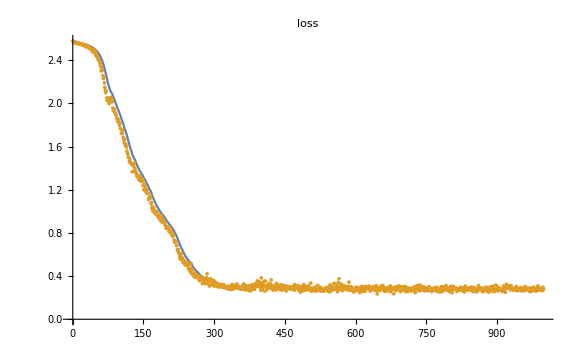
```mathematica
"Random vectors for new types and labels";
-Graphics-;
```

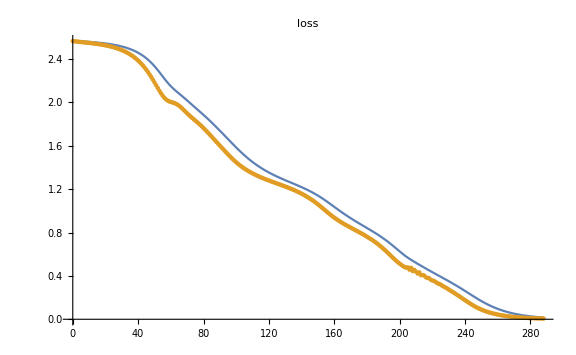
```mathematica
"New trainbale vectors for labels, a trainable vector for unknonw types";
-Graphics-;
```

```mathematica
"abnormal spike in loss";
```

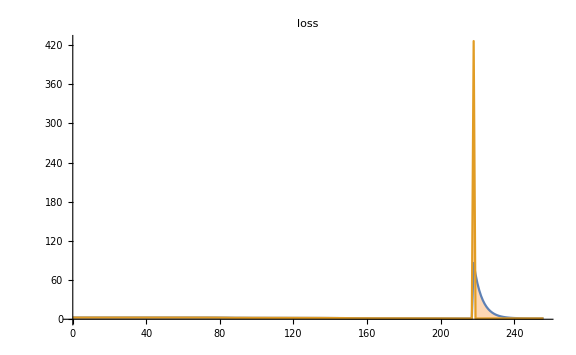
```mathematica
-Graphics-;
```